```mathematica
SetOptions[$FrontEnd, "ClearEvaluationQueueOnKernelQuit" -> False]
```

## NicePlots

```mathematica
Quit[];
```

```mathematica
testName = First@NotebookRead[PreviousCell[CellStyle -> "Section"]];
```

```mathematica
testFileName=FileNameJoin[{DirectoryName[NotebookDirectory[],1],testName<>".wlt"}];
pacletDir=DirectoryName[testFileName,2];
PacletDirectoryLoad[pacletDir];
testContextBase=FileBaseName[testFileName];
$ContextPath=Cases[$ContextPath,Except["PacletizedResourceFunctions`"]];
```

```mathematica
Needs["FernandoDuarte`LongRunRisk`"];
```

```mathematica
model=Models["NRC"];
```

```mathematica
momF =UncondE;
var = nombondyield[t,m];
maxMaturity=24;
varF=momF@var
```

```mathematica
solWc=FernandoDuarte`LongRunRisk`ComputationalEngine`SolveEulerEq`updateCoeffs[model,"UpdatePd"->True];
```

```mathematica
ToNum["Rules",model];
```

```mathematica
ToNum["Rules",model,"MaxMaturity"->1];
```

```mathematica
ReleaseHold@If[KeyExistsQ[model["extraInfo"],"initialGuess"],"initialGuess"->model["extraInfo"]["initialGuess"],Hold@Sequence[] ]
```

```mathematica
FernandoDuarte`LongRunRisk`Tools`ToNumber`Private`toNumRules[model,"MaxMaturity"->1,{}]
```

```mathematica
FernandoDuarte`LongRunRisk`Tools`ToNumber`Private`toNumRules[model,"MaxMaturity"->1,{} ,"initialGuess"-><|"Ewc"->{4.6},"Epd"->{{0,15},{0,15},{5.5}}|>]
```

```mathematica
dataF=Table[{m,varF}/.m->mm,{mm,maxMaturity}]//ToNum[model,{},solWc,"MaxMaturity"->24,"UpdateBonds"->True]
```

```mathematica
Dynamic
```

```mathematica
ListLinePlot[dataF]
```

```mathematica
paramNumRange=<|
	alpha->{0.005,0.15,0.01},
	tau->{0.1,4,0.05},
	beta->{0.001,0.1,0.005},
	av->{0.01,0.15,0.01},
	gamma->{1,10,0.5},
	kappa->{0.1,2,0.1},
	muG->{-1,1,0.1},
	kappaG->{0.01,2,0.1},
	sigmaG->{-0.3,0.3,0.001},
	X0->{1,10000,250},
	g0->{-5,5,0.2},
	z0->{-5,5,1},
	varepsilon->{1,3,0.25},
	phi0->{-0.1,0.5,0.005},
	phig->{-0.2,0.2,0.005},
	phiz->{-0.2,0.2,0.005},
	gmin->{-2,2,0.1},
	gmax->{-2,6,0.1},
	T->{1,5,1}
|>;
```

```mathematica
toParamRange=Map[{#[[1]],#[[2]],(#[[2]]-#[[1]])/20}&,Flatten/@((N@(toParam//.toParam/.Map[Interval@Most@#&,paramNumRange]))/.Interval[x_]->List[x])];
paramRange=Join[paramNumRange,toParamRange];

paramDyn={phig,phi0,muG,sigmaG,kappaG,alpha,tau,beta,av,gmin,gmax};
paramDynAssoc=param[[Key[#]&/@paramDyn]];





varNamesTeXAssoc=(Association@Thread[varNames->varNamesTeX]);
irfControls={
{{gminIRF,-0.5,"gminIRF"},-6,3,0.1,Appearance->{"Open",Small}},
{{gmaxIRF,0.12,"gmaxIRF"},-3,6,0.1,Appearance->{"Open",Small}},
{{g0min,-0.15,"g0minIRF"},-6,6,0.1,Appearance->{"Open",Small}},
{{g0med,0.09,"g0medIRF"},-6,6,0.1,Appearance->{"Open",Small}},
{{g0max,0.11,"g0maxIRF"},-6,6,0.1,Appearance->{"Open",Small}}
};

paramStatControls=KeyValueMap[{{ToExpression[ToString[#1]<>"M"],#2,ToString[#1]},paramRange[#1]/.List->Sequence,Appearance -> {"Open",Small}}&,paramDynAssoc];

parControls=Join[paramStatControls,irfControls];
```

```mathematica
SetOptions[$FrontEnd, "ClearEvaluationQueueOnKernelQuit" -> True]
```

```mathematica
Manipulate[

,

Evaluate[Sequence@@parControls]
,
ContinuousAction->None
]
```

```mathematica
Quit[];
```

```mathematica
testName = First@NotebookRead[PreviousCell[CellStyle -> "Section"]];
```

```mathematica
testFileName=FileNameJoin[{DirectoryName[NotebookDirectory[],1],testName<>".wlt"}];
pacletDir=DirectoryName[testFileName,2];
PacletDirectoryLoad[pacletDir];
testContextBase=FileBaseName[testFileName];
$ContextPath=Cases[$ContextPath,Except["PacletizedResourceFunctions`"]];
resourcesDir=FileNameJoin[{pacletDir,"Resources"}];
Get@Get[FileNameJoin[{resourcesDir,"Models.wl"}]];
```

```mathematica
Needs["FernandoDuarte`LongRunRisk`Tools`ToNumber`"]
Needs["FernandoDuarte`LongRunRisk`Tools`NicePlots`"]
(*Needs["FernandoDuarte`LongRunRisk`"]*)
```

```mathematica
myModel=FernandoDuarte`LongRunRisk`Models["NRCStochVol"];
```

```mathematica
newparams={delta->0.999,Esg->0.000062,Esp->0.01,gamma->15,muc->0.0016,mup->0.0033,mupbar->0.0033,phic->0.0021,phicp->0.002,phig->0.0029,phip->-0.0025,phipbarpb->1.1,phispw->1.81*^-7,psi->1.5,rhocp->0.2,rhog->0.998,rhopbar->0.9,rhoppbar->1,vp->0.9795,vpp->-7/100000,vppbar->7/1000000,xic->-0.198,xip->0.00073,mud[1]->0.0016,phidc[1]->0.0021,phidp[1]->0.002,rhodp[1]->0.2,xid[1]->-0.198};
solNew= toNum["Rules", myModel,newparams,{}];
```

FindRoot::reged: The point {4.38902} is at the edge of the search region {0.,4.38902} in coordinate 1 and the computed search direction points outside the region.

```mathematica
solWcNew=FilterRules[solNew,FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[_]]
```

{FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[0]→4.38902,FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[1]→0.140843,FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[2]→-0.066,FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[3]→0.000101555,FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[4]→0.139369,FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[5]→-8.74681,FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[6]→1.1861,FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[7]→-1072.81}

A[0]  4.38902

FindRoot::reged: The point {4.38902} is at the edge of the search region {0.,4.38902} in coordinate 1 and the computed search direction points outside the region.

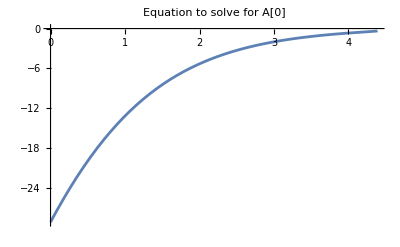

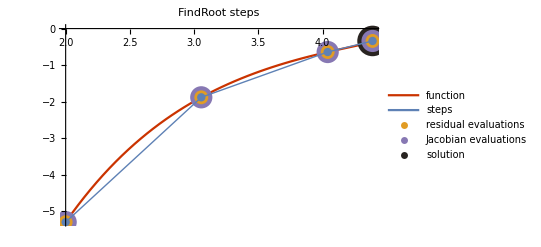

```mathematica
(*FindRoot plot to find A[0]*)
Echo[FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[0]/.solWcNew,"A[0]"];
plotNew=plotCoeffs[myModel,solWcNew,newparams,{2}, PlotLegends->Automatic];
Show[Plot@@(Rest@Append[plotNew,PlotLabel->"Equation to solve for A[0]"])]
Show[First@plotNew, PlotLabel->"FindRoot steps"]
```